## Kapitola 15 - LVQ a Iris data

Demonstrace použití LVQ neuronové sítě na datech z databáze UCI.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Import dat

### Načtení dat ze souboru

Nastavíme si pracovní adresář na ten, kde máme uložen aktuální notebook, načítaná data musejí být ve stejném adresáři.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dokumenty\ŠKOLA\ČVUT\BP\BP_Neuron

```mathematica
data=Import["iris.data"];
```

### Načtení dat přímo z internetu

Jiná možnost je importovat data přímo z internetu - příklad pro UCI databázi (stejná data jako v předchozím příkladu - načtení dat ze souboru).

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

## Předzpracování dat

Provedeme předzpracování dat pomocí stejného postupu, jaký je popsán v kapitole “Dopředná síť a Iris data”.

```mathematica
data2=Drop[data,-1];
inData=data2[[All,1;;4]];(*vstupní parametry*)
outDataTmp=data2[[All,5]];(*výstupní parametr*)
outVal=Tally[outDataTmp][[All,1]];
encode=MapIndexed[#1->Normal[SparseArray[#2->1,{Length[outVal]}]]&,outVal];
outData=Flatten[outDataTmp]/.encode;
```

## Zpracování dat neuronovou sítí

Nejdříve se podíváme na rozložení jednotlivých skupin vzorků v datech. Následující příkaz vykreslí vstupní data a jejich množství v jednotlivých třídách.

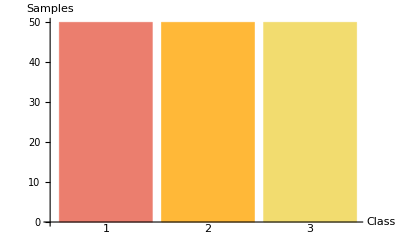

```mathematica
NetClassificationPlot[inData, outData, DataFormat -> BarChart, BarStyle -> {Hue[.4], Hue[.5], Hue[.6]}]
```

Názornější pohled na 3 a vícedimenzionální data lze zobrazit pomocí roznásobení vstupních vektorů s vektory zobrazovaného prostoru. Na problém, jak nejlépe zvolit tyto vektory, je nejlepším řešením vyzkoušení různých variant a vybrat tu, ve které jsou data nejlépe separována.

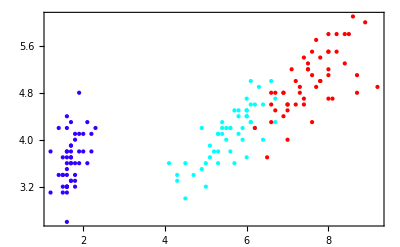

```mathematica
NetClassificationPlot[inData . {{0,0},{0,1},{1,0},{1,1}},outData,PlotStyle->{Hue[.7],Hue[.5],Hue[.0]}]
```

Vstupní data namapujeme sítí, jejíž uspořádání můžeme zadat. Čím víc neuronů použijeme, tím bude lépe pokryt prostor vstupních dat. Číslo 5 udává počet neuronů. Poslední číslo v příkazu udává počet iterací, není nutné ho uvádět, poté proběhne 6 iterací. Z vykresléného grafu je nejlépe poznat potřebná hodnota.

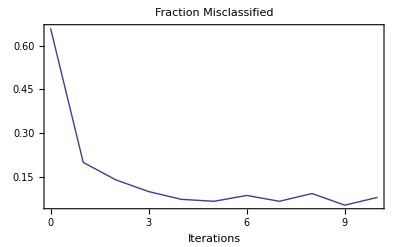

VQFit::DeadNeuron: Some codebook vectors are not used by the data. They have 'died' during the training. Use UnUsedNeurons to identify them and decide if you want to remove them.

```mathematica
{vq, fitrecord} = VQFit[inData, outData, 5, 10];
```

Varovná hláška říká, že některé neurony nejsou využity pro klasifikaci. V další části se tedy podíváme, které to jsou a odstraníme je, abychom neměli zbytečně velkou síť. Předtím se však ještě podívejme na průběh učení. Síť, která dokonale odpovídá na vstupní data, má všechny vzorky na úhlopříčce.

```mathematica
NetPlot[fitrecord,inData,outData,DataFormat->BarChart]
```

-Graphics-

Nyní odebereme nepotřebné neurony.
Nejprve si zobrazíme informace o síti, což se nám bude hodit po odebrání neuronů pro porovnání sítě.

```mathematica
NetInformation[vq]
```

VQ network for 3 classes with {2, 2, 1} codebook vectors per class, altogether 5. It takes data vectors with 4 components. Created 2011-4-5 at 21:31.

Zjistíme, které neurony jsou nepoužité.

```mathematica
UnUsedNeurons[vq,inData]
```

{{1},{},{}}

Vybereme je.

```mathematica
neuronyNaSmazani=Flatten[
MapIndexed[
{radek,#}&/@#1/.radek->#2⟦1⟧&,
UnUsedNeurons[vq,inData]
],1
]
```

{{1,1}}

A smažeme.

```mathematica
vq=NeuronDelete[vq,neuronyNaSmazani]
```

VQ[{-Codebook Vectors-},{CreationDate → {2011, 4, 5, 21, 31, 33.0225134}, AccumulatedIterations → 10}]

Nyní si znovu zobrazíme informace o síti a vidíme, že se odebrání povedlo.

```mathematica
NetInformation[vq]
```

VQ network for 3 classes with {1, 2, 1} codebook vectors per class, altogether 4. It takes data vectors with 4 components. Created 2011-4-5 at 21:31.

A takto vypadá klasifikace naučené sítě.

```mathematica
NetPlot[vq,inData,outData,CbvSymbol->{FontSize->30}]
```

-Graphics3D-

Získaná síť může být použita na mapování jakýchkoliv vektorů (se správnou dimenzí, shodnou se vstupními vektory sítě). Výstup ukazuje, ke kterému referenčnímu vektoru má nejblíže. V příkladu jsou použity vektory za vstupních dat, obecně se dají použít jakákoliv data.

```mathematica
vq[{{6.4,2.9,4.3,1.3},{6.9,3.2,5.7,2.3}}]
```

{{0,1,0},{0,0,1}}

Další příkazem zjistíme procentuální neúspěšnost klasifikace. Příkaz vrátí procento chybně klasifikovaných vektorů.

```mathematica
VQPerformance[vq,inData,outData] *100
```

8.

Dále si můžeme nechat zobrazit průměrnou vzdálenost mezi vstupními vektory a váhovými vektory. Čím menší je hodnota, tím lépe odpovídá síť datům.

```mathematica
VQDistance[vq,inData]
```

0.66056

Pokud je pokrytí už velmi dobré, můžeme také nechat projít algoritmus učení opakovaně.  Při volbě Recursive -> False je délka kroku učícího algoritmu nastavena na jedničku pro všechny iterace, což se hodí právě pro situace, kdy jsou váhové vektory blízko svým optimálním hodnotám. Pro vektory vzdálené svému optimu může být tento způsob nestabilní.  Zatímco při Recursive -> True (výchozí hodnota) je délka kroku v prvních iteracích malá, takže váhové vektory najdou správnou orientaci. Poté je krok zvětšen, pro urychlení pokrytí. Od této vysoké hodnoty se délka kroku opět pomalu snižuje. Pokrytí je zaručeno, když se délka kroku blíží nule.
Nejdříve se podíváme jak dopadne nenaučená síť s jednotlivými volbami.

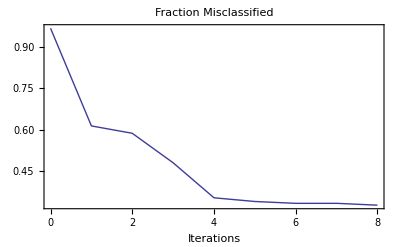

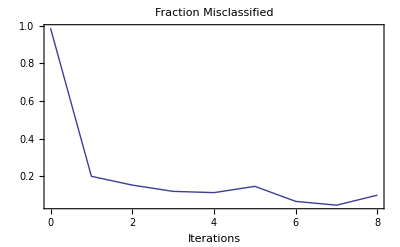

VQFit::DeadNeuron: Some codebook vectors are not used by the data. They have 'died' during the training. Use UnUsedNeurons to identify them and decide if you want to remove them.

```mathematica
{f,fiterecord} = VQFit[inData, outData, 4, 8, Recursive->False];
{t,fiterecord} = VQFit[inData, outData, 4, 8, Recursive->True];
```

Doučení sítě, která byla vytvořena s parametrem Recursive -> False, nejprve opět s Recursive -> False, poté s hodnotou True.

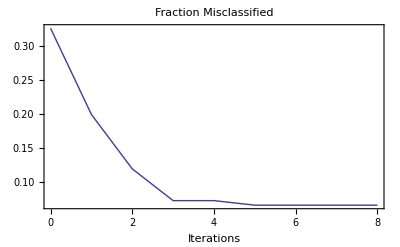

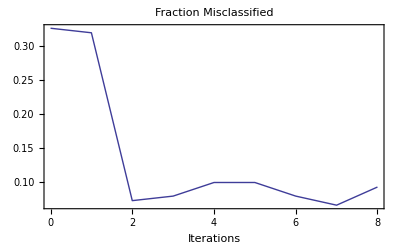

VQFit::DeadNeuron: Some codebook vectors are not used by the data. They have 'died' during the training. Use UnUsedNeurons to identify them and decide if you want to remove them.

```mathematica
ff = VQFit[inData, outData, f, 8, Recursive->False];
ft = VQFit[inData, outData, f, 8, Recursive->True];
```

A doučení sítě, která byla vytvořena s parametrem Recursive -> True, nejprve  Recursive -> True, poté s hodnotou False.

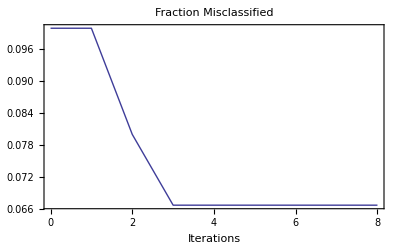

VQFit::DeadNeuron: Some codebook vectors are not used by the data. They have 'died' during the training. Use UnUsedNeurons to identify them and decide if you want to remove them.

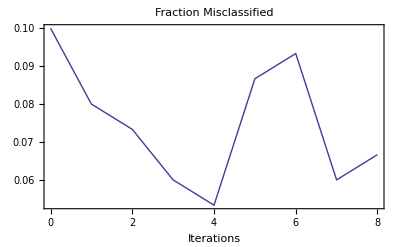

VQFit::DeadNeuron: Some codebook vectors are not used by the data. They have 'died' during the training. Use UnUsedNeurons to identify them and decide if you want to remove them.

```mathematica
tf = VQFit[inData, outData, t, 8, Recursive->False];
tt = VQFit[inData, outData, t, 8, Recursive->True];
```

## Vizualizace výstupu sítě

BarChart ve 3D zobrazení ukazuje správně klasifikované vektory a jejich počet na diagonále. Nesprávně klasifikované vektory jsou mimo ni.

```mathematica
NetPlot[vq,inData,outData,DataFormat->BarChart]
```

-Graphics3D-

2D BarChart nejlépe vypovídá o tom do které třídy naše síť klasifikuje kolik dat.

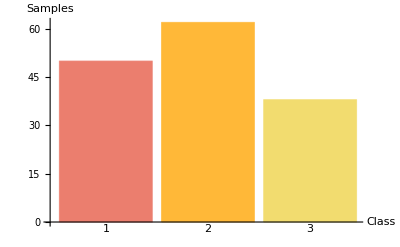

```mathematica
NetPlot[vq,inData,DataFormat->BarChart]
```

Zobrazení pomocí tabulky také vypovídá o rozložení vektorů do jednotlivých tříd. Vidímě díky ní také jaké data síť do které třídy klasifikuje. 2:50 znamená že je do této třídy klasifikováno 50 vektorů ze třídy 2.

```mathematica
NetPlot[vq, inData, outData, DataFormat -> Table]
```

VQ Classification |  | 
1:50 | 2:50
3:12 | 3:38

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.